# Exact Quasisymmetry

## Quasisymmetry Equations

```mathematica
(*σ'[s]-sigmap[s]=0*)
sigmap[s_]=Flatten@(-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2);
(*psi'-psiMatA[s]psi[s]-psiMatB[s]=0*)
psiMatA[s_]=({{-3 F0 σ[s]+(2 k'[s])/k[s], (5 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+3 α'[s], (3 k'[s])/k[s], 3/2 ((F0 ηb^2)/k[s]^2+(F0 k[s]^2 (1+σ[s]^2))/ηb^2+2 α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], F0 σ[s]-(2 k'[s])/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(3 F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-3 α'[s], (3 k'[s])/k[s]}, {-F0 σ[s]+k'[s]/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-α'[s], 0, 3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], -F0 σ[s]+k'[s]/k[s], -3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s]), 0}});
psiMatB[s_]=1/(B0 c0)Flatten@({{({{(B0 c0 (2 F0^2 k[s]^8 σ[s]^5 (3 F0 ηb^2-k[s]^2 α'[s])+2 F0 k[s]^4 σ[s]^3 (4 F0^2 ηb^6+2 k[s]^6 (ηb^2-F0 α'[s])+2 ηb^2 k[s]^2 (k'[s]^2+5 F0 ηb^2 α'[s])+ηb^2 k[s]^4 (5 F0^2-3 α'[s]^2)+ηb^2 k[s]^3 k''[s])+F0 k[s]^7 σ[s]^4 (k'[s] (-8 F0 ηb^2+2 k[s]^2 α'[s])+k[s]^3 α''[s])+k[s] (4 ηb^6 k'[s]^3+6 F0 ηb^8 k'[s] α'[s]-2 k[s]^8 k'[s] (ηb^2-F0 α'[s])+ηb^2 k[s]^4 k'[s] (ηb^4-4 k'[s]^2-8 F0 ηb^2 α'[s])+3 ηb^2 k[s]^5 k'[s] k''[s]+F0 k[s]^9 α''[s]-6 ηb^6 k[s]^3 α'[s] α''[s]+6 ηb^2 k[s]^7 α'[s] α''[s]-k[s] (3 ηb^6 k'[s] k''[s]+F0 ηb^8 α''[s])+ηb^6 k[s]^2 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^6 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-k[s]^5 σ[s]^2 (2 k[s]^4 k'[s] (ηb^2-2 F0 α'[s])+4 ηb^2 k'[s] (k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^5 α''[s]-6 ηb^2 k[s]^3 α'[s] α''[s]+k[s] (-3 ηb^2 k'[s] k''[s]+4 F0 ηb^4 α''[s])+ηb^2 k[s]^2 (2 k'[s] (5 F0^2-α'[s]^2)+Derivative[3][k][s]))+σ[s] (2 F0^3 ηb^10-2 F0 k[s]^10 (-2 ηb^2+F0 α'[s])+2 F0 ηb^6 k[s]^2 (4 k'[s]^2+7 F0 ηb^2 α'[s])+ηb^2 k[s]^8 (4 F0^3+3 ηb^2 α'[s]-6 F0 α'[s]^2)+2 k[s]^4 (-2 ηb^4 k'[s]^2 α'[s]+3 F0 ηb^6 (F0^2+3 α'[s]^2))-2 F0 ηb^6 k[s]^3 k''[s]+2 F0 ηb^2 k[s]^7 k''[s]+4 ηb^4 k[s]^5 (2 α'[s] k''[s]+k'[s] α''[s])+2 k[s]^6 (2 F0 ηb^2 k'[s]^2+ηb^4 (2 F0 ηb^2+8 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])))))/(2 ηb^4 k[s]^7)}})}, {({{(B0 c0 (4 F0^3 ηb^12+4 F0 ηb^8 k[s]^2 (3 k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^12 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^4 (6 F0^3 ηb^8 σ[s]^2-2 ηb^6 k'[s]^2 α'[s]+F0 ηb^8 (F0^2+7 α'[s]^2))+2 F0 k[s]^11 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s]^3 (2 F0 σ[s] k'[s]+k''[s])+2 ηb^2 k[s]^8 (-2 F0^3 ηb^2+2 F0^3 ηb^2 σ[s]^4-(ηb^4-2 k'[s]^2) α'[s]-8 F0 ηb^2 α'[s]^2+2 σ[s]^2 α'[s] (k'[s]^2-8 F0 ηb^2 α'[s])+12 ηb^2 σ[s] α'[s] α''[s])-4 k[s]^5 (4 ηb^4 σ[s] k'[s] (k'[s]^2+2 F0 ηb^2 α'[s])-ηb^6 (2 α'[s] k''[s]+k'[s] α''[s]))+2 ηb^2 k[s]^9 (8 F0 σ[s]^3 k'[s] α'[s]+σ[s] k'[s] (ηb^2+8 F0 α'[s])-2 (2 α'[s] k''[s]+k'[s] α''[s])-2 σ[s]^2 (2 α'[s] k''[s]+k'[s] α''[s]))-4 ηb^4 k[s]^7 (4 F0^2 σ[s]^3 k'[s]-F0 k''[s]-F0 σ[s]^2 k''[s]+σ[s] (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-ηb^2 k[s]^10 (24 F0^2 σ[s]^4 α'[s]-8 F0 σ[s] α''[s]-8 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (3 F0 ηb^2+36 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^6 (4 F0 (-3+σ[s]^2) k'[s]^2+12 σ[s] k'[s] k''[s]+ηb^2 (-3 F0 ηb^2+4 F0^2 (-1+2 σ[s]^2) α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))))/(4 ηb^4 k[s]^9)}})}, {({{(B0 c0 (2 F0^3 ηb^10 σ[s]+2 F0 k[s]^9 (1+σ[s]^2)^2 k'[s] α'[s]-ηb^2 k[s]^5 k'[s] (ηb^4+4 (1+σ[s]^2) k'[s]^2+4 F0 ηb^2 (1+σ[s]^2) α'[s])-2 k[s] (2 ηb^6 k'[s]^3+3 F0 ηb^8 k'[s] α'[s])+ηb^6 k[s]^2 (2 F0 σ[s] (2 k'[s]^2+F0 ηb^2 α'[s])+3 k'[s] k''[s]+F0 ηb^2 α''[s])+F0 k[s]^10 (1+σ[s]^2) (-2 F0 σ[s]^3 α'[s]+σ[s] (ηb^2-2 F0 α'[s])+α''[s]+σ[s]^2 α''[s])+2 ηb^6 k[s]^4 (2 F0^3 σ[s]^3+2 σ[s] (F0^3-F0 α'[s]^2)+3 α'[s] α''[s])+ηb^2 k[s]^8 (2 F0^3 σ[s]^5+σ[s] (2 F0^3+ηb^2 α'[s]-4 F0 α'[s]^2)+4 σ[s]^3 (F0^3-F0 α'[s]^2)+6 α'[s] α''[s]+6 σ[s]^2 α'[s] α''[s])+ηb^2 k[s]^6 (4 F0 σ[s]^3 k'[s]^2+2 F0 σ[s] (ηb^4+2 k'[s]^2)+3 k'[s] k''[s]+2 F0 ηb^2 α''[s]+σ[s]^2 (3 k'[s] k''[s]+2 F0 ηb^2 α''[s]))-ηb^6 k[s]^3 (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^7 (1+σ[s]^2) (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])))/(2 ηb^4 k[s]^7)}})}, {({{-(B0 c0 (4 F0^3 ηb^12+k[s]^2 (-8 F0^2 ηb^4 k[s]^5 σ[s] (1+σ[s]^2) k'[s]+4 F0 ηb^8 (3 k'[s]^2+4 F0 ηb^2 α'[s])+2 F0 k[s]^10 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^2 (F0^3 ηb^8 (5+6 σ[s]^2)-2 ηb^6 k'[s]^2 α'[s]+7 F0 ηb^8 α'[s]^2)+2 ηb^2 k[s]^6 (2 F0^3 ηb^2 (2+5 σ[s]^2+3 σ[s]^4)+(ηb^4-2 (1+σ[s]^2) k'[s]^2) α'[s]+6 F0 ηb^2 (1+σ[s]^2) α'[s]^2)-2 F0 k[s]^9 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s] (2 F0 σ[s] k'[s]+k''[s])+4 ηb^6 k[s]^3 (2 α'[s] (-F0 σ[s] k'[s]+k''[s])+k'[s] α''[s])+2 ηb^2 k[s]^7 (ηb^2 σ[s] k'[s]-4 F0 σ[s] k'[s] α'[s]-4 F0 σ[s]^3 k'[s] α'[s]+4 α'[s] k''[s]+4 σ[s]^2 α'[s] k''[s]+2 (1+σ[s]^2) k'[s] α''[s])+ηb^2 k[s]^8 (16 F0^2 σ[s]^4 α'[s]-4 F0 σ[s] α''[s]-4 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (F0 ηb^2+28 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^4 (12 F0 (1+σ[s]^2) k'[s]^2+ηb^2 (3 F0 ηb^2+4 F0^2 (7+8 σ[s]^2) α'[s]-4 α'[s]^3-4 F0 σ[s] α''[s]+2 Derivative[3][α][s])))))/(4 ηb^4 k[s]^9)}})}});
(*psi2[s]-psi32[s]=0*)
psi32[s_]=1/(B0 c0)1/(4 F0 ηb^2 k[s]^6)B0 c0 (4 F0^3 ηb^6 k[s] σ[s]+4 F0^2 ηb^6 k'[s]-2 k[s]^6 k'[s] (ηb^2+2 F0 (1+σ[s]^2) α'[s])+4 k[s]^2 (2 ηb^2 k'[s]^3+F0 ηb^4 k'[s] α'[s])-4 F0 ηb^2 k[s]^4 (F0 (1+σ[s]^2) k'[s]-σ[s] k''[s])+2 ηb^2 k[s]^3 (2 F0 σ[s] (-k'[s]^2+3 F0 ηb^2 α'[s])-4 k'[s] k''[s]-3 F0 ηb^2 α''[s])+F0 k[s]^7 (ηb^2 σ[s]+4 F0 (σ[s]+σ[s]^3) α'[s]-2 (1+σ[s]^2) α''[s])+4 ηb^2 k[s]^5 (F0^3 (σ[s]+σ[s]^3)+2 F0 σ[s] α'[s]^2-2 α'[s] α''[s]));
```

## Residual and Jacobian Functions

```mathematica
Clear[f,df,optsPsi1,optsPsi2,optsPsi3];
optsPsi1={k[s]->psi[6],k'[s]->cup[psi[6]],k''[s]->cupp[psi[6]],k'''[s]->cuppp[psi[6]],α'[s]->to,α''[s]->top,α'''[s]->topp,σ[s]->psi[5],F0->psi[7],ηb->etabb};
optsPsi2={cup[psi[6]]->cup,cupp[psi[6]]->cupp,cuppp[psi[6]]->cuppp,Table[psip[i,psi[i]]->psip[[i]],{i,1,5}]}//Quiet//Flatten;
optsPsi3={Table[{psi[i]->psi1[[i]],D[psip[i,psi[i]],psi[i]]->dpsidpsi},{i,1,7}],D[cup[psi[6]],psi[6]]->dpsidpsi,D[cupp[psi[6]],psi[6]]->cpsipp,D[cuppp[psi[6]],psi[6]]->cpsippp}//Flatten//Quiet;
f1={
{psip[1,psi[1]],psip[2,psi[2]],psip[3,psi[3]],psip[4,psi[4]]}-(psiMatA[s].{psi[1],psi[2],psi[3],psi[4]}+psiMatB[s]),
psip[5,psi[5]]-sigmap[s],
psi[2]-psi32[s]
(*σ[0]-sigma0*)
}/.optsPsi1//Flatten;
df[etabb_,to_,top_,topp_,psi1_,psip_,dpsidpsi_,cpsipp_,cpsippp_,cup_,cupp_,cuppp_]=Simplify[Table[D[f1,psi[i]],{i,1,7}]/.optsPsi2/.optsPsi3]//Transpose//Quiet;
f[etabb_,to_,top_,topp_,psi1_,psip_,cup_,cupp_,cuppp_]=Simplify[f1/.optsPsi2/.optsPsi3];
```

## Residual and Jacobian Matrices

```mathematica
Clear[fres,Jfres];
fres=Compile[{{nss,_Integer},{Dmat1,_Real,2},{Dmat2,_Real,2},{Dmat3,_Real,2},{psii,_Real,1},{etabar,_Real},{torsMat,_Real,2},{sigma0,_Real}},
psimat=Table[Dmat1.psii[[(i-1)nss+1;;i nss]],{i,1,5}]; (*Derivatives of psi*)
cupMat=Dmat1.psii[[5nss+1;;6nss]]; (*First Derivative of Curvature*)
cuppMat=Dmat2.psii[[5nss+1;;6nss]]; (*Second Derivative of Curvature*)
cupppMat=Dmat3.psii[[5nss+1;;6nss]]; (*Third Derivative of Curvature*)
fmattemp=Table[f[etabar,torsMat[[i,1]],torsMat[[i,2]],torsMat[[i,3]],{psii[[i]],psii[[nss+i]],psii[[2nss+i]],psii[[3nss+i]],psii[[4nss+i]],psii[[5nss+i]],psii[[6nss+1]]},psimat[[All,i]],cupMat[[i]],cuppMat[[i]],cupppMat[[i]]],{i,1,nss}];
Append[Transpose[fmattemp,{2,1}]//Flatten,psii[[5nss]]-sigma0],
CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable},Parallelization->True
];
Jfres=Compile[{{nss,_Integer},{Dmat1,_Real,2},{Dmat2,_Real,2},{Dmat3,_Real,2},{psii,_Real,1},{etabar,_Real},{torsMat,_Real,2},{sigma0,_Real}},
firstDer=Dmat1;secondDer=Dmat2;thirdDer=Dmat3; (*Derivative Matrices*)
psimat=Table[firstDer.psii[[(i-1)nss+1;;i nss]],{i,1,5}]; (*Derivatives of psi*)
cupMat=firstDer.psii[[5nss+1;;6nss]]; (*First Derivative of Curvature*)
cuppMat=secondDer.psii[[5nss+1;;6nss]]; (*Second Derivative of Curvature*)
cupppMat=thirdDer.psii[[5nss+1;;6nss]]; (*Third Derivative of Curvature*)
Jfmattemp=ParallelTable[
df[
etabar,torsMat[[i,1]],torsMat[[i,2]],torsMat[[i,3]],
{psii[[i]],psii[[nss+i]],psii[[2nss+i]],psii[[3nss+i]],psii[[4nss+i]],psii[[5nss+i]],psii[[6nss+1]]},
psimat[[All,i]],firstDer[[i,j]],secondDer[[i,j]],thirdDer[[i,j]],
cupMat[[i]],cuppMat[[i]],cupppMat[[i]]
],{i,1,nss},{j,1,nss}];
Jfsigmarow=Table[KroneckerDelta[i,5nss]1,{i,1,6nss+1}];
Jmat1=Drop[Flatten[Table[Table[Table[Jfmattemp[[All,j,i,k]],{i,1,6}]//Flatten,{j,1,nss}],{k,1,7}],1]//Transpose,0,-(nss-1)];
Jmat=Insert[Jmat1,Jfsigmarow,6nss+1],
{{Jfmat1,_Real,2},{Jfmattemp,_Real,4},{Jmat,_Real,2}},
CompilationTarget->"C",RuntimeAttributes->{Listable},RuntimeOptions->"Speed",Parallelization->True
];
```

## Solve System of Equations

```mathematica
solveQS[nIts_,tol_,nLineS_,etab_,ns_,sigma0_,psiIn_]:=Module[
{deltaold=0,delta=(2 π)/ns },
(*Initial Arrays*)
psiInit=Append[Table[psiIn[delta t][[1;;6]],{t,1,ns}]//Transpose//Flatten,psiIn[s][[8]]];
torsMat=Table[{psiIn[delta t][[7]],psiIn'[delta t][[7]],psiIn''[delta t][[7]]},{t,1,ns}];
(*Derivative Matrix*)
column11=Prepend[ Table[ 0.5 (-1)^n Cot[n/2 delta],{n,1,ns-1}],0];
column22=RotateRight[Reverse[column11]];
Dmat1=ToeplitzMatrix[column11,column22];
Dmat2=Dmat1.Dmat1;Dmat3=Dmat1.Dmat2;
(*Solve for Psi*)
psii=psiInit;
For[i=1,i≤nIts,i++,
{f1,Jacf1}=Chop[Re[{fres[ns,Dmat1,Dmat2,Dmat3,psii,etab,torsMat,sigma0],Jfres[ns,Dmat1,Dmat2,Dmat3,psii,etab,torsMat,sigma0]}]];
deltay=Check[-LinearSolve[Jacf1,f1],False,LinearSolve::nosol]//Quiet;
If[deltay==False,Break[],deltay=Chop[deltay]];
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiiTemp=psii+deltay;
{f2,Jacf2}=Chop[Re[{fres[ns,Dmat1,Dmat2,Dmat3,psiiTemp,etab,torsMat,sigma0],Jfres[ns,Dmat1,Dmat2,Dmat3,psiiTemp,etab,torsMat,sigma0]}]];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
psii=psiiTemp;
deltaold=deltay;
];
{psii,Table[res[i],{i,1,nIts}]}
]
```

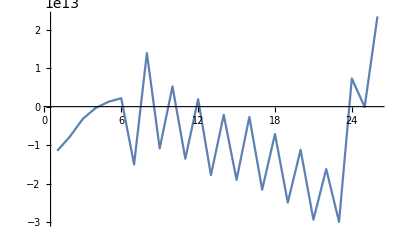

-Graphics-

```mathematica
ns=26;etabar=0.5;nfp=2;sigma0=0;nIts=12;tol=10^-4;nLineS=2;
psiIn[s_]={
0.01Sin[nfp s],(*psi31*)
0.01Sin[nfp s],(*psi32*)
0.01Cos[nfp s],(*psi33*)
0.01Sin[nfp s], (*psi34*)
0.01Cos[nfp s], (*sigma*)
1+0.Cos[nfp s], (*curvature*)
0.0Sin[nfp s], (*torsion*)
0.1  (*F0*)
};
sol=solveQS[nIts,tol,nLineS,etabar,ns,sigma0,psiIn];
ListLinePlot[sol[[1,5ns+1;;6ns]],PlotRange->All]
ListLinePlot[sol[[2]]]
```